```mathematica
b[n_]:=((n(4n-1)(4n-3))/(2(2n+1)))^(1/4)
```

```mathematica
A[n_]:=√((b[n]^(4n-1)Gamma[2n])/(Gamma[1/2]Gamma[(4n-1)/2]))
```

```mathematica
ψ[n_,x_]:=A[n]/((x^2+b[n]^2)^n)
```

```mathematica
ψGround[x_]:=1/π^(1/4)ⅇ^(-x^2/2)
```

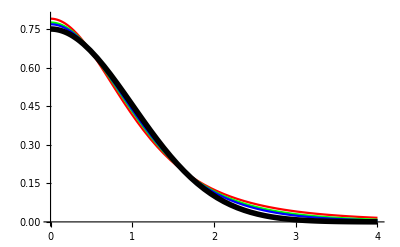

```mathematica
Plot[{ψ[2,x],ψ[3,x],ψ[4,x],ψGround[x]},{x,0,4},PlotRange->{0,0.8},PlotStyle->{Red,Green,Blue,{Black,Thickness[0.01]}}]
```

```mathematica
c[n_]:=((n(4n-3)(4n-5))/(2(2n+1)))^(1/4)
```

```mathematica
B[n_]:=√((c[n]^(4n-3)Gamma[2n])/(Gamma[3/2]Gamma[(4n-3)/2]))
```

```mathematica
ψ1[n_,x_]:=(B[n]x)/((x^2+c[n]^2)^n)
```

```mathematica
ψFirst[x_]:=(√2)/π^(1/4)x ⅇ^(-x^2/2)
```

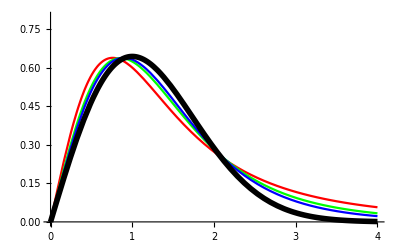

```mathematica
Plot[{ψ1[2,x],ψ1[3,x],ψ1[4,x],ψFirst[x]},{x,0,4},PlotRange->{0,0.8},PlotStyle->{Red,Green,Blue,{Black,Thickness[0.01]}}]
```